```mathematica
SetDirectory[NotebookDirectory[]]
PacletDirectoryAdd[{"/Users/ianfan/Downloads/WolframSummerSchoolRL-master"}];
<<WolframSummerSchoolRL`;
PacletDirectoryAdd[{"/Users/ianfan/Downloads/neuralnetworks"}]
<<NeuralNetworks`
Lookup[PacletInformation@"NeuralNetworks","Version"]
Get["RLproject-pong-q-duo.wl"]
Get["/Users/ianfan/Documents/gym-http-api/binding-wl/gym_http_client.wl"];
```

/Users/ianfan/Documents/gym-http-api/binding-wl

{/Users/ianfan/Downloads/WolframSummerSchoolRL-master,/Users/ianfan/Downloads/neuralnetworks}

11.3.7

## Nets

```mathematica
policyNet=NetInitialize@NetChain[{LinearLayer[128],Tanh,LinearLayer[128],Tanh,LinearLayer[2]},"Input"->8,"Output"->NetDecoder[{"Class",{0,1}}]];
data = preprocess[game[10,10000,policyNet,True,0,$env]];
Length[data["reward"]]
```

717

```mathematica
$env=RLEnvironmentCreate["WLCartPole"]
```

RLEnvironment[…]

```mathematica
generator := creatGenerator[$env, 20, 10000, False, 0.98, 1000, 0.95]
```

## Training

RLEnvironment[…]

```mathematica
net = Import["8k-net.wlnet"]
```

NetChain[<>]

```mathematica
trained = NetTrain[policyNet, generator,LossFunction->MeanSquaredLossLayer[],BatchSize->32,MaxTrainingRounds->2000]
```

NetChain[<>]

```mathematica
quitEnv[]
```

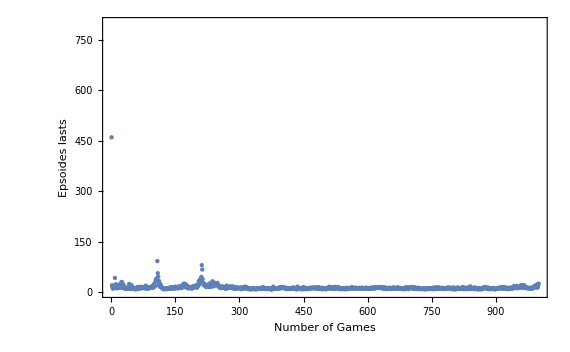

```mathematica
$rewardList;
ListPlot[$rewardList,PlotRange->800,Frame->True, FrameLabel->{"Number of Games","Epsoides lasts"}]
```

```mathematica
RLEnvironmentClose[$env]
```

```mathematica
bN = getBest[];
data = preprocess[game[1,10000,bN,True,0,$env]];
Length[data["action"]]
```

10000

```mathematica
data = preprocess[game[10,10000,net,True,0,$env]];
Length[data["action"]]
```

1

```mathematica
preprocess[game["Pong-ram-v0",10,10000,policyNet,True,0]]
```

<|action→{3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,728,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3},2,1|>
 |  |  |  |

```mathematica
data =generator[<|"AbsoluteBatch"->0,"BatchSize"->12,"Net"->policyNet|>];
```

```mathematica
data["Input"][[2]]
```

{0.000143174,-0.162165,-0.0370522,0.211108,0.00730161,-0.357922,-0.0474192,0.518349}

```mathematica
Length[data["Input"]]
```

12

```mathematica
x
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
game["Pong-ram-v0",1,10,policyNet,True,0]
```

```mathematica
Quit
```

```mathematica
re = {};

ob = RLEnvironmentReset[$env];
pre = ob;
Do[
pre = Join[ob,pre];
action = net[pre];
pre = ob;
state = RLEnvironmentStep[$env, action, True];
ob = state["Observation"];
AppendTo[re,state["Rendering"]];
If[state["Done"],Break[]];
,{step,10000}];
```

```mathematica
ListAnimate[re[[;;500]],120]
```

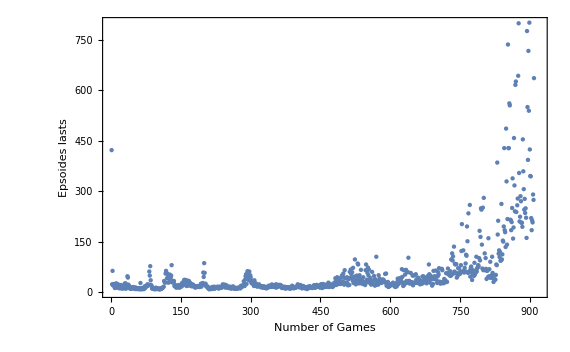

```mathematica
$env=RLEnvironmentCreate["Pong-v0"]
```